```mathematica
n=300;
```

```mathematica
data2 =Table[0.0,n,500,18];
```

```mathematica
data3 = data2 ;
```

```mathematica
data3[[3]] ={data2[[2]]} ;//AbsoluteTiming
```

{0.0432838,Null}

```mathematica
data3[[3]] =data2[[2]] ;//AbsoluteTiming
```

{0.0134969,Null}

```mathematica
Dimensions[data3]
```

{300,500,18}

```mathematica
List@@data3//Dimensions
```

{300,500,18}

```mathematica
TableForm[{ {Null,"ByteCount", "LeafCount"},{"data2", ByteCount[data2], LeafCount[data2]},{"data3", ByteCount[data3], LeafCount[data3]}}]
```

Null | ByteCount | LeafCount
data2 | 21600160 | 2850301
data3 | 72989696 | 2840801

```mathematica
Dimensions[data2]
```

{300}

```mathematica
data= RandomReal[1,{n,{500,18}}];
```

RandomReal::array: The array dimensions {300,{500,18}} given in position 2 of RandomReal[1,{300,{500,18}}] should be a list of non-negative machine-sized integers giving the dimensions for the result.

```mathematica
data2 = data;
```

```mathematica
i = RandomInteger[{1,n},10];
```

```mathematica
data3 = data2;
```

```mathematica
i[[1]]
```

{13}

```mathematica
@@
```

```mathematica
Length[data3]
```

300

```mathematica
Length[i]
```

3

```mathematica
data3[[i]] =Nothing
```

Set::pkspec1: The expression {{13},{250},{121}} cannot be used as a part specification.

Nothing

```mathematica
Dimensions[data2]
```

{300,500,18}

```mathematica
Length[data3]
```

300

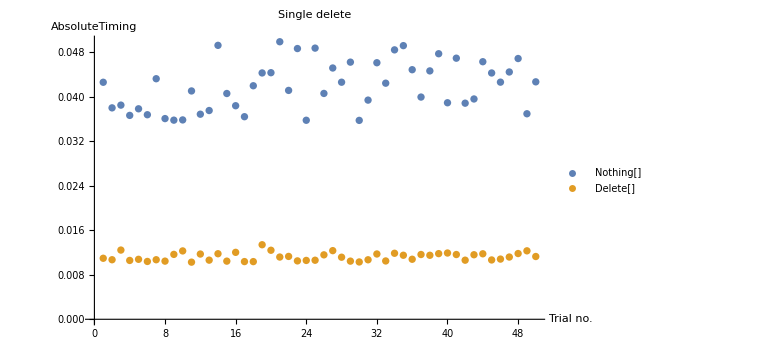

```mathematica
timing ={{"Nothing[]","Delete[]"}};
For[j=0,j<50, j++,
data3=data2;
i = RandomInteger[{1,n},{10,1}];
ii = Flatten[i];
t1 = AbsoluteTiming[data3[[ii]]=Nothing;];
data3=data2;
t2 = AbsoluteTiming[Delete[data3, i];];
AppendTo[timing,{First[t1],First[t2]}]
]
ListPlot[{timing[[2;;,1]],timing[[2;;,2]]},ImageSize->Large, PlotLegends->timing[[1]],AxesLabel->{"Trial no.","AbsoluteTiming"}, PlotLabel->"Single delete"]
```

```mathematica
LeafCount[data2]
```

2850301

```mathematica
LeafCount[data3]
```

2850301

```mathematica
LeafCount[data2]
```

2840801

```mathematica
ByteCount[data2]
```

72989696

```mathematica
ByteCount[data3]
```

21600160

```mathematica
Dimensions[data3[[1]]]
```

{500,18}

```mathematica
AbsoluteTiming[data3=Delete[data3, i];]
```

Delete::partw: Part {266} of … does not exist.

{1.2926,Null}

```mathematica
Dimensions[data2]
```

{300,500,18}

```mathematica
ii
```

{13,250,121}

```mathematica
i
```

{{13},{250},{121}}

```mathematica
data3=data2;
i =  {{13}, {250}, {121}};
ii = Flatten[i];
t1 = AbsoluteTiming[data3[[ii]]=Nothing; data3=data3;];
```

```mathematica
data3//Length
```

297

```mathematica
i
```

{{13},{250},{121}}

```mathematica
Length[data3]
```

```mathematica
data3
```

Removed[$$Failure]

```mathematica
Dimensions[data2]
```

{300,500,18}